# My glucose series

## Program

```mathematica
getTimeSer[gs_]:=Module[{tr},
tr=Transpose[gs];
TimeSeries[tr[[2]],{tr[[1]]}]]
```

```mathematica
getMarkPos[ser_]:=Position[ser,{_,_,{_String}}]
```

```mathematica
getMarkedDate[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
Map[#[[1]]&,ser[[pos]]]
]
```

```mathematica
getMarkedItem[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
ser[[pos]]
]
```

```mathematica
timeShift=2209021200
```

2209021200

```mathematica
(* createEpilog[gs_]:=Map[Text["*",{UnixTime[#]+timeShift,80}]&,getMarkedDate[gs]] *)
```

```mathematica
createEpilog[gs_]:=Map[Text[#[[3]],{UnixTime[#[[1]]]+timeShift,80}]&,getMarkedItem[gs]]
```

## Data

```mathematica
gs=Get["/Users/kouamano/Profile/blood-glc.txt"]
```

{{Thu 3 Feb 2022 06:05:00GMT+9,148,{}},{Thu 3 Feb 2022 11:16:00GMT+9,396,{}},{Thu 3 Feb 2022 16:31:00GMT+9,257,{}},{Fri 4 Feb 2022 06:06:00GMT+9,177,{}},{Fri 4 Feb 2022 11:16:00GMT+9,273,{}},{Fri 4 Feb 2022 18:30:00GMT+9,204,{}},{Sat 5 Feb 2022 05:57:00GMT+9,98,{}},{Sat 5 Feb 2022 12:15:00GMT+9,137,{}},{Sat 5 Feb 2022 17:15:00GMT+9,226,{}},{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Sun 6 Feb 2022 12:21:00GMT+9,374,{}},{Sun 6 Feb 2022 17:28:00GMT+9,241,{}},{Mon 7 Feb 2022 06:17:00GMT+9,158,{}},{Mon 7 Feb 2022 11:34:00GMT+9,293,{}},{Mon 7 Feb 2022 16:44:00GMT+9,382,{}},{Tue 8 Feb 2022 06:23:00GMT+9,152,{}},{Tue 8 Feb 2022 12:09:00GMT+9,399,{}},{Tue 8 Feb 2022 17:05:00GMT+9,275,{}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Wed 9 Feb 2022 11:54:00GMT+9,348,{}},{Wed 9 Feb 2022 17:04:00GMT+9,271,{}},{Thu 10 Feb 2022 06:21:00GMT+9,216,{}},{Thu 10 Feb 2022 11:54:00GMT+9,133,{}},{Thu 10 Feb 2022 17:01:00GMT+9,264,{}},{Fri 11 Feb 2022 06:25:00GMT+9,191,{}},{Fri 11 Feb 2022 12:00:00GMT+9,197,{}},{Fri 11 Feb 2022 17:04:00GMT+9,224,{}},{Sat 12 Feb 2022 06:23:00GMT+9,165,{}},{Sat 12 Feb 2022 12:09:00GMT+9,210,{}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}},{Sun 13 Feb 2022 06:17:00GMT+9,217,{}},{Sun 13 Feb 2022 12:27:00GMT+9,286,{}},{Sun 13 Feb 2022 17:23:00GMT+9,300,{}},{Mon 14 Feb 2022 06:12:00GMT+9,211,{}},{Mon 14 Feb 2022 12:18:00GMT+9,245,{}},{Mon 14 Feb 2022 18:49:00GMT+9,204,{}},{Tue 15 Feb 2022 06:18:00GMT+9,199,{}},{Tue 15 Feb 2022 11:59:00GMT+9,287,{}},{Tue 15 Feb 2022 18:21:00GMT+9,205,{}},{Wed 16 Feb 2022 06:15:00GMT+9,226,{}},{Wed 16 Feb 2022 12:16:00GMT+9,308,{}},{Wed 16 Feb 2022 18:27:00GMT+9,242,{}},{Thu 17 Feb 2022 06:21:00GMT+9,238,{}},{Thu 17 Feb 2022 12:07:00GMT+9,209,{}},{Thu 17 Feb 2022 19:06:00GMT+9,210,{}},{Fri 18 Feb 2022 06:11:00GMT+9,190,{}},{Fri 18 Feb 2022 12:12:00GMT+9,288,{}},{Fri 18 Feb 2022 19:21:00GMT+9,211,{}},{Sat 19 Feb 2022 06:13:00GMT+9,231,{}},{Sat 19 Feb 2022 12:17:00GMT+9,231,{}},{Sat 19 Feb 2022 17:55:00GMT+9,179,{}},{Sun 20 Feb 2022 06:52:00GMT+9,217,{}},{Sun 20 Feb 2022 12:20:00GMT+9,243,{}},{Sun 20 Feb 2022 17:42:00GMT+9,244,{}},{Mon 21 Feb 2022 06:20:00GMT+9,197,{}},{Mon 21 Feb 2022 12:07:00GMT+9,206,{}},{Mon 21 Feb 2022 19:04:00GMT+9,195,{}}}

```mathematica
nPoints=Length[gs]
```

57

```mathematica
getMarkPos[gs]
```

{{10},{19},{30}}

```mathematica
getMarkedDate[gs]
```

{Sun 6 Feb 2022 06:08:00GMT+9,Wed 9 Feb 2022 05:52:00GMT+9,Sat 12 Feb 2022 17:09:00GMT+9}

```mathematica
getMarkedItem[gs]
```

{{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}}}

Basic points

```mathematica
startTime=UnixTime[gs[[1,1]]]+timeShift
endTime=UnixTime[gs[[-1,1]]]+timeShift
```

3852857100

3854459040

Period

```mathematica
period=(endTime-startTime)/nPoints//N
```

28104.2

```mathematica
gts=getTimeSer[gs]
```

TimeSeries[…]

```mathematica
createEpilog[gs]
```

{Text[{*},{3853116480,80}],Text[{*},{3853374720,80}],Text[{*},{3853674540,80}]}

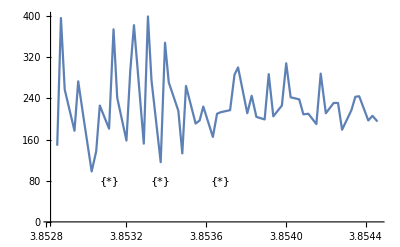

```mathematica
ListLinePlot[gts,Epilog->createEpilog[gs]]
```

Shift

```mathematica
1643835900-3852857100
```

-2209021200

Interpolation

```mathematica
Interpolation[gts]
```

InterpolatingFunction[…]

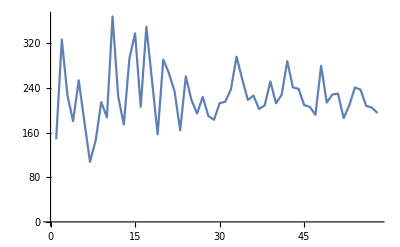

```mathematica
ListLinePlot[Table[Interpolation[gts][t],{t,startTime,endTime,period}]]
```

Fourier(1)

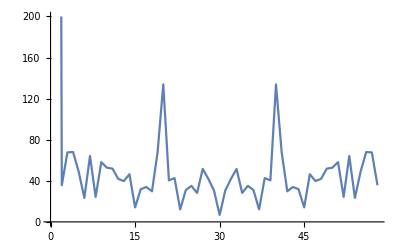

```mathematica
ListLinePlot[Fourier[Table[Interpolation[gts][t],{t,startTime,endTime,period}]]//Abs,PlotRange->{All,{0,200}}]
```

Fourier(2)

InterpolatingFunction::dmval: 入力値{3.8537×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3.85373×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3.85376×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

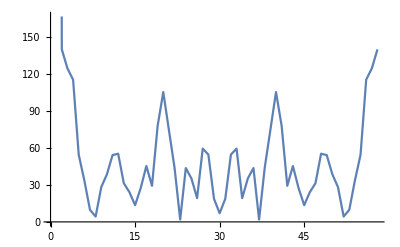

```mathematica
ListPlot[Fourier[InterpolatingFunction[…][Range[startTime,endTime,period]]//N]//Abs,Joined->True]
```

## TimeSeries[]の時刻はなんの時刻か？

UnixTime[]そのものは正しい

```mathematica
Date[]
```

{2022,2,23,16,13,19.903623}

```mathematica
UnixTime[] (* date +%s の値と同じ *)
```

1645600453

```mathematica
UnixTime[Date[]]
```

1645600455

https://keisan.casio.jp/exec/system/1526003938 の値ともおなじ。

[不思議 その1] しかし、UnixTimeとDateObjectとの関係がおかしい：

```mathematica
DateObject[0-UnixTime[0],TimeZone->"Japan"]
```

Thu 1 Jan 1970 09:00:00JST

```mathematica
DateObject[0-UnixTime[0],TimeZone->"UTC"] (* UTCを指定したのに+9時間進んでいる *)
```

Thu 1 Jan 1970 09:00:00UTC

とにかく、DateObjectに変換したときにシフトする、TimeSeries[]もこれを踏襲する

```mathematica
DateObject[0]
```

Mon 1 Jan 1900 00:00:00GMT+9

```mathematica
UnixTime[0]
```

-2209021200

```mathematica
gts//Length
```

4

```mathematica
gs[[1]][[1]]//UnixTime
```

1643835900

```mathematica
gs[[-1]][[1]]//UnixTime
```

1645437840

```mathematica
gts[[2]]
```

{{{148,396,257,177,273,204,98,137,226,181,374,241,158,293,382,152,399,275,116,348,271,216,133,264,191,197,224,165,210,213,217,286,300,211,245,204,199,287,205,226,308,242,238,209,210,190,288,211,231,231,179,217,243,244,197,206,195}},{{{3852857100,3852875760,3852894660,3852943560,3852962160,3852988200,3853029420,3853052100,3853070100,3853116480,3853138860,3853157280,3853203420,3853222440,3853241040,3853290180,3853310940,3853328700,3853374720,3853396440,3853415040,3853462860,3853482840,3853501260,3853549500,3853569600,3853587840,3853635780,3853656540,3853674540,3853721820,3853744020,3853761780,3853807920,3853829880,3853853340,3853894680,3853915140,3853938060,3853980900,3854002560,3854024820,3854067660,3854088420,3854113560,3854153460,3854175120,3854200860,3854239980,3854261820,3854282100,3854328720,3854348400,3854367720,3854413200,3854434020,3854459040}}},1,{Continuous,1},{Discrete,1},1,{ResamplingMethod→{Interpolation,InterpolationOrder→1},ValueDimensions→1}}

```mathematica
gts[[2]][[2]][[1]][[1]][[1]]
```

3852857100

2209021200のシフトとは？ -> 1900年 1月 1日を紀元としている

```mathematica
gts[[2]][[2]][[1]][[1]][[1]]-(gs[[1]][[1]]//UnixTime)
```

2209021200

```mathematica
gts[[2]][[2]][[1]][[1]][[-1]]-(gs[[-1]][[1]]//UnixTime)
```

2209021200

```mathematica
DateObject[3852857100]
```

Thu 3 Feb 2022 06:05:00GMT+9

```mathematica
DateObject[0]
```

Mon 1 Jan 1900 00:00:00GMT+9

[不思議 その2] 1900 年を紀元とするカレンダーとは？

```mathematica
??CalendarType
```

''' CalendarTypepaclet:ref/CalendarTypeは，デフォルトで，"Gregorian"に設定されている． '''

''' CalendarTypepaclet:ref/CalendarTypeのデフォルト値はAutomaticpaclet:ref/Automaticで，これは，0年がない初期のグレゴリオ暦を使う．西暦以前の年は負で，以後は正である． '''